## Exercise 1

### Using Mathematica

```mathematica
iseq = y == a[i, y, f, q];
lmeq = m == l[i, y];
derivs = {Dt[iseq], Dt[lmeq]};
notationRules = {Dt[q]->dQ,Dt[f]->dF,Dt[y]->dY,Dt[i]->di, Dt[m] -> dm, Derivative[0,0,0,1][a][i,y,f,q]->Subscript[a, q],Derivative[0,0,1,0][a][i,y,f,q]->Subscript[a, f],Derivative[0,1,0,0][a][i,y,f,q]->Subscript[a, y],Derivative[1,0,0,0][a][i,y,f,q]->Subscript[a, i],Derivative[0,1][l][i,y]->Subscript[l, y],Derivative[1,0][l][i,y]->Subscript[l, i]};
derivs/.notationRules // FullSimplify // MatrixForm//TraditionalForm
Solve[derivs, {Dt[q], Dt[m]}]/.notationRules // FullSimplify // TraditionalForm
```

(dF a_f+di a_i+dQ a_q+dY a_y==dY
dm==di l_i+dY l_y)

{{dQ→-(dF a_f+di a_i+dY (a_y-1))/a_q,dm→di l_i+dY l_y}}

### Using Matrix Methods

(A_q | 0
-L_y | 1) (dQ
dm) = (A_F dF + A_i di  + (1-A_y)dY
L_i di + L_y dY)

```mathematica
cInverse = Inverse[({{Subscript[A, q], 0}, {-Subscript[L, y], 1}})]
```

{{1/A_q,0},{L_y/A_q,1}}

```mathematica
cInverse .  ({{Subscript[A, F] dF + Subscript[A, i] di  + (1-Subscript[A, y])dY}, {Subscript[L, i] di + Subscript[L, y] dY}}) // MatrixForm // TraditionalForm
```

```mathematica
({{(dF Subscript[A, F]+di Subscript[A, i]+dY (1-Subscript[A, y]))/Subscript[A, q]}, {(Subscript[L, y] (dF Subscript[A, F]+di Subscript[A, i]+dY (1-Subscript[A, y])))/Subscript[A, q]+di Subscript[L, i]+dY Subscript[L, y]}})
```

The sign of (∂Q)/(∂F) is obtained by solving the above for (∂Q)/(∂F) (that is holdiing all the other partials constant). We obtain (∂Q)/(∂F) = -A_F/A_Q. We assume that A_Q > 0 and A_F > 0.  We obtain (∂Q)/(∂F) < 0.

## Exercise 2

```mathematica
Maximize[{c1^(1/2)+c2^(1/2), c1*1+3*c2 ≤ 10000}, {c1, c2}]
```

{200/(√3),{c1→7500,c2→2500/3}}

Using the substituttion method
We solve (c_1 + 3*c_2 = 10000) for c_1 to obtain (c_1 = 10000 - 3 c_2)
Substituting into the utility function, we obtain:
U(c_2) = (10000 - 3 (c_2))^(1/2) + c_2^(1/2)
U’ = -3/2(10000 - 3 (c_2))^(-1/2)+ 1/2 c_2^(-1/2) = 0
c_2 = 2500/3
Substituting into c_1 = 10000 - 3 c_2
c_1 = 7500


Using Langrangian method
ℒ = c_1^(1/2) + c_2^(1/2) + λ (c_1 + 3 c_2 - 10000)
(∂ℒ)/(∂λ) = c_1 + 3 c_2 - 10000 = 0
(∂ℒ)/(∂c_1) = 1/2 c_1^(-1/2) + λ c_1 = 0
(∂ℒ)/(∂c_2) = 1/2 c_2^(-1/2) + 3λ c_2 = 0
c_1 = 7500
c_2 = 2500/3

## Exercise 3

The identity relation on any set x is the set {(x, x) | x ∈ X}. It is
1. Reflexive. Because all ∀_(x ∈ X), (x, x) ∈ i_x by definiction
2. Symmetric, becuase all members of the set of i_x are of the form (x, x).  Which means that ∀_(x, y ∈ X) (x, y) ∈ i_x ⇔ (y, x) ∈ i_y (because x = y)
3. Transitive. Because ∀_(x, y ∈ X)(x, y) ∈ i_x ⇒ x = y. ∴ (x, y) ∈ i_x ∧ (y, z) ∈ i_x ⇒ (x, z) ∈ i_x (since in this case y and z are also x)

## Exercise 4

The symmetric component I of relation R are the subset of R such that {(x, x’) ∈ I} ⇔ {(x’, x) ∈ I}.  We know the relation R is transitive, meaning ∀_(x,y, z ∈ X)({x, y) ∈ R} ∧ ({y, z) ∈ R} ⇔ {(x, z) ∈ R}.  For the symeetric component, we have the subset of R which is  {(x, x’) ∈ I} ⇔ {(x’, x) ∈ I}.  This is a tautology.

For the asymmetric component P, we have the subset of R such that {(x, x’) ∈ P} ⇒ {(x’, x) ∉ P}. We know the relation R is transitive, meaning ∀_(x,y, z ∈ X)({x, y) ∈ R} ∧ ({y, z) ∈ R} ⇔ {(x, z) ∈ R}.  For the asymettric component, we have the subset of R which is {(x, x’) ∈ P} ⇒ {(x’, x) ∉ P}.  Replacing y with x’, and noting the transitive nature of the original we obtain that ∀_(x,y ∈ X)({x, x’) ∈ R} ∧ ({x’, z) ∈ R} ⇔ {(x, z) ∈ R}

By symmetry and transitivity we can replace y in the relationship (x P y) ∧ (y I z) to obtain (x P z).  Similarly, by symmetry and transitivity, we can replace the second y in (x I y) ∧ (y P z) to obtain (x P z).

## Exercise 5

I is a transitive binary relation. Assume that (x, z) ∉ I.  Assume that (x, y) ∈ I ∧ (y, z) ∈ I.  By transitivity, we have (x, z) ∈ I.  But this is a contradiction. Thus we must  have (x, y) ∉ I ∨ (y, z) ∉ I ∧ (x, z) ∈ I.

## Exercise 6

R = {(1, 2), (1, 3), (1, 4), (1, 5), (1, 5), (1, 6), (1, 7), (1,8), (1, 9), (1, 10), (1, 11), (1, 12), (2, 4), (2, 6), (2, 8), (2, 10), (2, 12), (3, 6), (3, 9), (3, 12), (4, 8), (4, 12), (5, 10), (6, 12)}
We see that it is transitive because if x R y ∧ y R z ⇒ x R z (check each entry).  We can also see this numerically, because if a is divisible by b and b is divisible by c then a is divisible by c.

## Exercise 7

## Exercise 8

We ae given that R is reflexive and transitive.  The inverse relation R^-1 is given by {(y, x) ∈ R^-1| (x, y) ∈ R}.  The intersection of these two relations are the only elements that are symmetric.  Therefore it is an equivalence relation.

## Exercise 9

## Exercise 10

The transitive closure of R are R_t = {(g, q} ∈ P^2 | g is a grandparent of q or parent of q}.  The relationship R_t∘ R_t^-1 = ∅

## Exercise 11

1. X = {a, b, c}, R = {(a, a), (a, b), (c, b)}
In order to make the relation symmetric, we must add: (b, a) and (b, c).
R_s =  {(a, a), (a, b), (c, b), (b, a), (b, c)}
The transitive closure of this set is R_t = {(a, a), (a, b), (c, b), (b, b), (c, c), (a, c)}
The reflexive closure for this set is R_r=  {(a, a), (a, b), (c, b), (b, b), (c, c)}

2. The symmetric closure of this set is {(x, y) ∈ X^2 | x ≤ y}
The transitive closure is the original set
The reflexive closure is  {(x, y) ∈ X^2 | x ≤ y}

3.  This is the diagonal of width r.
The relationship is already reflexive and symmetric and transitive.

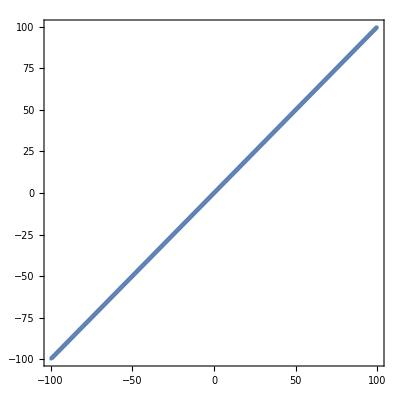

```mathematica
RegionPlot[Abs[j - k]  < 1, {j, -100, 100}, {k, -100, 100}]
```

## Execrise 12

## Computational Exercise 1

```mathematica
prefMatrix = {{1, 0, 0, 1}, {0, 0, 1, 1}, {0, 1, 1, 1}, {1, 1, 1, 0}}
```

{{1,0,0,1},{0,0,1,1},{0,1,1,1},{1,1,1,0}}

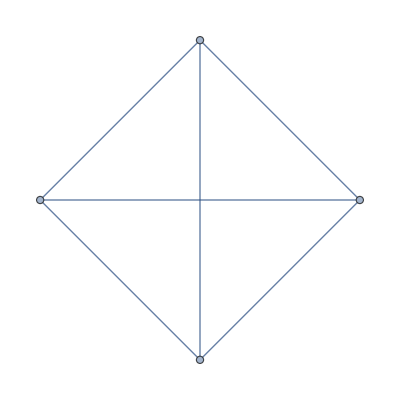

SparseArray[<12>, {4, 4}]

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

```mathematica
TransitiveClosureGraph[AdjacencyGraph[prefMatrix]]
AdjacencyMatrix[%]
%//MatrixForm
```

```mathematica
MatrixForm[prefMatrix]
```

(1 | 0 | 0 | 1
0 | 1 | 1 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 1)

## Computational Exercise 2

```mathematica
p = {{1.0, 1.0, 1.0}, {0.5, 2.0, 1.0}, {1.0, 1.0, 1.0}, {2.0, 0.5, 1.0}, {2.0, 0.5, 1.0}, {1.0, 1.0, 1.0}, {1.0, 1.0, 1.0}};
q = {{30, 9, 9}, {34, 10, 0}, {10, 4, 0}, {4, 8, 5}, {2, 15, 0}, {0, 15, 9}, {4, 7, 12}};
costx = p . Transpose[q] ;
%//MatrixForm
```

(48. | 44. | 14. | 17. | 17. | 24. | 23.
42. | 37. | 13. | 23. | 31. | 39. | 28.
48. | 44. | 14. | 17. | 17. | 24. | 23.
73.5 | 73. | 22. | 17. | 11.5 | 16.5 | 23.5
73.5 | 73. | 22. | 17. | 11.5 | 16.5 | 23.5
48. | 44. | 14. | 17. | 17. | 24. | 23.
48. | 44. | 14. | 17. | 17. | 24. | 23.)

```mathematica
rdMatrix = Table[0,{i,1,7},{j,1,7}]
Do[rdMatrix[[j, k]] = costx[[j, j]] ≥ costx[[j, k]], {j, Range[1, 7]}, {k, Range [1, 7]}]
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

```mathematica
rdMatrix = Boole[rdMatrix]
```

{{1,1,1,1,1,1,1},{0,1,1,1,1,0,1},{0,0,1,0,0,0,0},{0,0,0,1,1,1,0},{0,0,0,0,1,0,0},{0,0,1,1,1,1,1},{0,0,1,1,1,0,1}}

```mathematica
%//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 1)

```mathematica
prefFunc[p_, q_]:= Module[{costx,rdMatrix},costx = p . Transpose[q];
rdMatrix = Table[0, {i, 1, Length[p]}, {j, 1,  Length[q]}];
Do[rdMatrix[[j, k]] = Boole[costx[[j, j]] ≥ costx[[j, k]]], {j, Range[1, Length[rdMatrix]]}, {k, Range [1, Length[rdMatrix]]}];
rdMatrix]
```

```mathematica
prefFunc[p, q] // MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 1)

## Computational Exercise 3

See previous exercise.

```mathematica
(* To create the composition relation R ∘ R == R^2, we square the matrix R and then only pick those elements ≠ 0*) 
rdMatrix2 = MatrixPower[rdMatrix, 2]
Do[rdMatrix2[[j, k]] = Boole[rdMatrix2[[j, k]]≠ 0], {j, 1, Length[rdMatrix]}, {k, 1, Length[rdMatrix]}]
```

{{1,2,5,5,6,3,4},{0,1,3,3,4,1,2},{0,0,1,0,0,0,0},{0,0,1,2,3,2,1},{0,0,0,0,1,0,0},{0,0,3,3,4,2,2},{0,0,2,2,3,1,1}}

```mathematica
rdMatrix2//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1)

We see that rdMatrix 2 is a subset of rdMatrix